```mathematica
PMuSigma[mu_,σ_,bin_]:=Subscript[n, bin]^((Subscript[n, bin]+1)/2)/(√π 2^((Subscript[n, bin]-1)/2)Gamma[Subscript[n, bin]/2])Subscript[V, bin]^(Subscript[n, bin]/2)*σ^(-Subscript[n, bin]-2)Exp[-Subscript[n, bin]/(2 σ^2)((mu-Subscript[xMean, bin])^2+Subscript[V, bin])];

PSigma[σ_,bin_]:=Subscript[n, bin]^((Subscript[n, bin]-1)/2)/(2^((Subscript[n, bin]-3)/2)Gamma[(Subscript[n, bin]-1)/2])Subscript[V, bin]^((Subscript[n, bin]-1)/2)*σ^(-Subscript[n, bin])Exp[-(Subscript[n, bin] Subscript[V, bin])/(2 σ^2)];
```

```mathematica
fullFunc =1/kBT* PMuSigma[z1/kBT+(λ b1(b2-b1))/δ12,b1,1]*PSigma[b2,2];
Integrate[fullFunc,{λ,0,1}]
```

(2^(1/2 (3-n_1-n_2)) b1^(-2-n_1) b2^-n_2 ⅇ^(-(n_1 V_1)/(2 b1^2)-(n_2 V_2)/(2 b2^2)) δ12 (Erf[(√n_1 (z1/kBT-xMean_1))/(√2 b1)]-Erf[(√n_1 (z1/kBT+(b1 (-b1+b2))/δ12-xMean_1))/(√2 b1)]) n_1^(n_1/2) n_2^(1/2 (-1+n_2)) V_1^(n_1/2) V_2^(1/2 (-1+n_2)))/((b1-b2) kBT Gamma[n_1/2] Gamma[1/2 (-1+n_2)])

```mathematica
PMuSigma[z1/kBT,b1,1]
```

(2^(1/2 (1-n_1)) b1^(-2-n_1) ⅇ^(-(n_1 (V_1+(z1/kBT-xMean_1)^2))/(2 b1^2)) n_1^(1/2 (1+n_1)) V_1^(n_1/2))/(√π Gamma[n_1/2])

```mathematica
PSigma[b2,2]
```

(2^(1/2 (3-n_2)) b2^-n_2 ⅇ^(-(n_2 V_2)/(2 b2^2)) n_2^(1/2 (-1+n_2)) V_2^(1/2 (-1+n_2)))/Gamma[1/2 (-1+n_2)]

```mathematica
(* Check normalization of the inverse χ^2 function *)
NInvChi2[μ_,σ2_,μ1_,ν1_,κ1_,σ12_]:=√(κ1/(2 π))(ν1 σ12/2)^(ν1/2)/Gamma[ν1/2] σ2^(-(ν1+3)/2)Exp[-(κ1(μ1-μ)^2+ν1 σ12)/(2σ2)];
Integrate[NInvChi2[μ,σ2,μ1,ν1,κ1,σ12],{μ,-∞,∞},Assumptions->{ν1>=1,σ12>0,κ1>0,σ2>0}]
Integrate[%,{σ2,0,∞},Assumptions->{ν1>=1,σ12>0,κ1>0}]

Integrate[NInvChi2[μ,σ2,μ1,ν1,κ1,σ12],{σ2,0,∞},Assumptions->{ν1>=1,σ12>0,κ1>0,σ2>0,ν1 σ12+κ1 Re[(μ-μ1)^2]>0}]
Integrate[%,{μ,-∞,∞},Assumptions->{ν1>=1}]
```

(2^(-ν1/2) ⅇ^(-(ν1 σ12)/(2 σ2)) (ν1 σ12)^(ν1/2) σ2^(-1-ν1/2))/Gamma[ν1/2]

1

(√κ1 (ν1 σ12)^(ν1/2) (1/(κ1 (μ-μ1)^2+ν1 σ12))^((1+ν1)/2) Gamma[(1+ν1)/2])/(√π Gamma[ν1/2])

$Aborted

```mathematica
Integrate[NInvChi2[μ,σ2,μ1,ν1,κ1,σ12],{μ,-∞,∞},Assumptions->{σ12>0,κ1>0,σ2>0}]

Integrate[%,{σ2,0,∞},Assumptions->{σ12>0,κ1>0}]
```

(2^(-ν1/2) ⅇ^(-(ν1 σ12)/(2 σ2)) ((ν1 σ12)/σ2)^(ν1/2))/(σ2 Gamma[ν1/2])

ConditionalExpression[1,Re[ν1]>0]

```mathematica
(* Find the missing factor for the NInvChi2 in multiple observations case *)
NInvChi2[μ,σ2,μ1,ν1,κ1,σ12]/ ((1/(2π σ2))^(n/2)Exp[-(n(μ-xMean)^2+n V)/(2 σ2)])/.{μ1->xMean,κ1->n,ν1->n-3,σ12->n V/(n-3)};
Simplify[%,Assumptions->σ2>0]
```

(2 √n π^(1/2 (-1+n)) (n V)^(1/2 (-3+n)))/Gamma[1/2 (-3+n)]

```mathematica
(* Calculate the norm of the inverse χ^2 distribution *)
InvChi2Tmp[σ2_,νp_,σp2_]:=σ2^(-(νp+2)/2)Exp[-(νp σp2)/(2σ2)];
InvChi2[σ2_,νp_,σp2_]:=((νp σp2)/2)^(νp/2)/Gamma[νp/2] σ2^(-νp/2-1)Exp[-(νp σp2)/(2σ2)]
Integrate[InvChi2Tmp[σ2,νp,σp2],{σ2,0,∞}, Assumptions->{σp2>0,νp>0}];
1/%//Simplify

Integrate[InvChi2[σ2,νp,σp2],{σ2,0,∞}, Assumptions->{σp2>0,νp>0}]
```

(2^(-νp/2) (νp σp2)^(νp/2))/Gamma[νp/2]

1

```mathematica
(* Integrate the normalized N-InvChi2 over σ2 *)
```

```mathematica
Integrate[NInvChi2[μ,σ2,μ1,ν1,κ1,σ12],{σ2,0,∞},Assumptions->{ν1>-1,ν1 σ12>0,κ1>0,(μ-μ1)^2≥0}];
Simplify[%]
FullSimplify[%/(√(κ1/(π ν1 σ12))Gamma[(1+ν1)/2]/Gamma[ν1/2](1+(κ1(μ-μ1)^2)/(ν1 σ12))^(-(ν1+1)/2)),Assumptions->{ν1>0, σ12>0,κ1 (μ-μ1)^2>0,κ1 (μ-μ1)^2+ν1 σ12>0,Im[ν1]==0}]
```

(((ν1 σ12)/(κ1 (μ-μ1)^2+ν1 σ12))^(ν1/2) √(κ1/(π κ1 (μ-μ1)^2+π ν1 σ12)) Gamma[(1+ν1)/2])/Gamma[ν1/2]

(1/(κ1 (μ-μ1)^2+ν1 σ12))^((1+ν1)/2) (κ1 (μ-μ1)^2+ν1 σ12)^((1+ν1)/2)

```mathematica
NInvChi2[μ,σ2,μ1,ν1,κ1,σ12]
```

(2^(-1/2-ν1/2) ⅇ^(-(κ1 (-μ+μ1)^2+ν1 σ12)/(2 σ2)) √κ1 (ν1 σ12)^(ν1/2) σ2^(1/2 (-3-ν1)))/(√π Gamma[ν1/2])

```mathematica
(* Check if better first integrate out lambda *)
i1=Integrate[NInvChi2[λ g dt,σ2,μ1,ν1,κ1,σ12],{λ,0,1},Assumptions->{ν1>-1,ν1 σ12>0,κ1>0,(μ-μ1)^2≥0}]
```

(2^(-1-ν1/2) ⅇ^(-(ν1 σ12)/(2 σ2)) (ν1 σ12)^(ν1/2) σ2^(-1-ν1/2) (Erf[(κ1 (dt g-μ1))/(√2 √(κ1 σ2))]+Erf[(κ1 μ1)/(√2 √(κ1 σ2))]))/(dt g Gamma[ν1/2])

```mathematica
Integrate[i1,{σ2,0,∞}]
```

$Aborted

```mathematica
(* Check if σ first is better and integrate over λ *)
i3=Integrate[NInvChi2[λ g dt,σ2,μ1,ν1,κ1,σ12],{σ2,0,∞},Assumptions->{ν1>-1,ν1 σ12>0,κ1>0,(λ g dt-μ1)^2≥0}]
```

(√κ1 (ν1 σ12)^(ν1/2) (1/(κ1 (-dt g λ+μ1)^2+ν1 σ12))^((1+ν1)/2) Gamma[(1+ν1)/2])/(√π Gamma[ν1/2])

```mathematica
i4=Integrate[i3,{λ,0,1}]
```

ConditionalExpression[1/(√π Gamma[ν1/2])√κ1 (ν1 σ12)^(ν1/2) Gamma[(1+ν1)/2] (-(((1/(κ1 μ1^2+ν1 σ12))^(1/2 (-1+ν1)) ((κ1 μ1^2+ν1 σ12) Hypergeometric2F1[1,1-ν1/2,-1/2,-(κ1 μ1^2)/(ν1 σ12)]+(κ1 μ1^2 (-4+ν1)-ν1 σ12) Hypergeometric2F1[1,1-ν1/2,1/2,-(κ1 μ1^2)/(ν1 σ12)]))/(dt g κ1 μ1 (-1+ν1) ν1 σ12))-((1/(κ1 (-dt g+μ1)^2+ν1 σ12))^(ν1/2) ((dt^2 g^2 κ1-2 dt g κ1 μ1+κ1 μ1^2+ν1 σ12) Hypergeometric2F1[1,1-ν1/2,-1/2,-(κ1 (-dt g+μ1)^2)/(ν1 σ12)]+(dt^2 g^2 κ1 (-4+ν1)-2 dt g κ1 μ1 (-4+ν1)+κ1 μ1^2 (-4+ν1)-ν1 σ12) Hypergeometric2F1[1,1-ν1/2,1/2,-(κ1 (-dt g+μ1)^2)/(ν1 σ12)]))/(dt g κ1 (dt g-μ1) (-1+ν1) ν1 σ12 √(1/(dt^2 g^2 κ1-2 dt g κ1 μ1+κ1 μ1^2+ν1 σ12)))),(Im[(√ν1 √σ12)/(dt g √κ1)]>Re[μ1/(dt g)]||1+Im[(√ν1 √σ12)/(dt g √κ1)]<Re[μ1/(dt g)]||Im[μ1/(dt g)]+Re[(√ν1 √σ12)/(dt g √κ1)]≠0)&&(Im[(√ν1 √σ12)/(dt g √κ1)]+Re[μ1/(dt g)]>1||Im[(√ν1 √σ12)/(dt g √κ1)]+Re[μ1/(dt g)]<0||Im[μ1/(dt g)]≠Re[(√ν1 √σ12)/(dt g √κ1)])]

```mathematica
Clear[x]
Integrate[(1+x^2)^(-(νc+1)/2),{x,a,b}]
```

-a Hypergeometric2F1[1/2,(1+νc)/2,3/2,-a^2]+b Hypergeometric2F1[1/2,(1+νc)/2,3/2,-b^2]

```mathematica
(* Check norm for the prior of the new system *)
newPrior =Exp[-(κp(μp-(a+λ g1)dt)^2)/(2 σ1^2)-(κp(μp-(a+λ g2)dt)^2)/(2 σ2^2)-(κp(μp-(a+λ g3)dt)^2)/(2 σ3^2)];
Integrate[newPrior, {a,-∞,∞},Assumptions->{dt>0,σ1>0,σ2>0,σ3>0,κp>0}]
```

(ⅇ^(-(dt^2 κp λ^2 (-2 g1 g3 σ2^2+g3^2 (σ1^2+σ2^2)+g2^2 (σ1^2+σ3^2)+g1^2 (σ2^2+σ3^2)-2 g2 (g3 σ1^2+g1 σ3^2)))/(2 (σ2^2 σ3^2+σ1^2 (σ2^2+σ3^2)))) √(2 π))/(dt √(κp (1/σ1^2+1/σ2^2+1/σ3^2)))

```mathematica
Gamma[-1]
```

ComplexInfinity

```mathematica
func1=y^(-νp/2-3/2)Exp[-((dx-(a+λ g)dt)^2+νp σp2)/(2 y)]
Integrate[func1, {y,0,∞},Assumptions->{νp σp2+Re[(a dt-dx+dt g λ)^2]>0,νp>0}]
```

ⅇ^(-((dx-dt (a+g λ))^2+νp σp2)/(2 y)) y^(-3/2-νp/2)

2^((1+νp)/2) ((a dt-dx+dt g λ)^2+νp σp2)^(1/2 (-1-νp)) Gamma[(1+νp)/2]

```mathematica
Gamma[(1+νp)/2]/Gamma[νp/2]
```

Gamma[(1+νp)/2]/Gamma[νp/2]

```mathematica
A0=(2 √n0 π)/(Gamma[(n0-3)/2](π n0 σ02)^((3-n0)/2));
fn =A0(1/(2 π σ2))^(n0/2)Exp[-(n0(μ-μ0)^2+n0 σ02)/(2 σ2)];
Integrate[fn,{μ,-∞,∞},Assumptions->{σ2>0,n0>0}]
Integrate[%,{σ2,0,∞},Assumptions->{σ02>0,n0>3}]
```

(2^(3/2-n0/2) ⅇ^(-(n0 σ02)/(2 σ2)) σ02^(1/2 (-3+n0)) (n0/σ2)^(1/2 (-1+n0)))/(n0 Gamma[1/2 (-3+n0)])

1

```mathematica
ⅇ^(-(n0 (-dxMean+μ0)^2+n0 σ02)/(2 σ2)) (2 π)^(-n0/2) (1/σ2)^(n0/2)
```

```mathematica
Integrate[fn,{σ2,0,∞},Assumptions->{Re[V+(dxMean-μ)^2]>0,n>0}]
(*Integrate[%,{μ,-∞,∞}]*)
```

ConditionalExpression[1/2 π^(-n/2) (n (V+(dxMean-μ)^2))^(1-n/2) Gamma[-1+n/2],n>2]

```mathematica
Gamma[0]
```

ComplexInfinity

```mathematica
Integrate[fn/.{μ->0,n->3},{σ2,0,∞}]
```

ConditionalExpression[1/(2 √3 π √(dxMean^2+V)),Re[dxMean^2+V]>0]

```mathematica
fn;
Integrate[2/(n0 σ02 Gamma[n0/2-1])((n0 σ02)/(2 σ2))^(n0/2)Exp[-(n0 σ02)/(2 σ2)],{σ2,0,∞},Assumptions->{σ02>0,n0>3}]
```

1

```mathematica
r1=Integrate[Exp[-(na(μ-μa)^2+ na σa2)/(2 σ2)],{μ,-∞,∞},Assumptions->{σ2>0,na>0}]
```

ⅇ^(-(na σa2)/(2 σ2)) √(2 π) √(σ2/na)

```mathematica
r2=Integrate[r1 (1/(2 π σ2))^(na/2),{σ2,0,∞},Assumptions->{n+na>4,σa2>0}]
```

ConditionalExpression[1/2 √(1/na) π^(1/2-na/2) (na σa2)^(3/2-na/2) Gamma[1/2 (-3+na)],na>3]

```mathematica
rules1={n1->n0+n,μ1->(n dxMean+n0 μ0)/(n+n0),σ12->(n dxMean^2+n0 μ0^2+n V+n0 σ02)/n1-μ1^2};

n(μ-dxMean)^2+n0(μ-μ0)^2+n V+n0 σ02-(n1(μ-μ1)^2+n1 σ12)//.rules1//FullSimplify
```

0

```mathematica
Clear[A0]
Integrate[A0(1/(2 π σ2))^(n0/2)Exp[-(n0 σ02)/(2 σ2)],{σ2,0,∞},Assumptions->{n0 σ02>0,n0>2}]
```

1/2 A0 π^(-n0/2) (n0 σ02)^(1-n0/2) Gamma[-1+n0/2]

```mathematica
Integrate[(1+y^2)^(1-n0/2),y]
```

y Hypergeometric2F1[1/2,-1+n0/2,3/2,-y^2]

```mathematica
Integrate[1/(√(2π σ2))Exp[-x^2/(2 σ2)],{x,-B,B}]
```

Erf[B/(√2 √σ2)]

```mathematica
Solve[Erf[B/(√2 √σ2)]==0.95,B]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{B→1.95996 √σ2}}

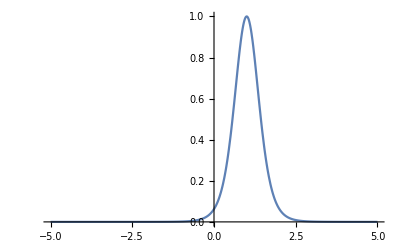

```mathematica
f2=(1+(z-z0)^2)^(1-n0/2)/.{z0->1,n0->10};
Plot[f2,{z,-5,5},PlotRange->All]
```